# Lab_Work_7

# Статистический анализ

```mathematica
1.Элементарная описательная статистика
```

```mathematica
data = RandomReal[50,10]
```

{33.7464,24.4723,42.5904,23.3918,48.7439,19.0489,9.9796,13.304,33.2643,1.57287}

```mathematica
(*Mean - находит среднее значение*)
Mean[data]
```

25.0114

```mathematica
(*Median - находит медиану, центральный элемент в отсортированной версии списка или среднее значение двух центральных элементов,если список имеет четную длину*)
Median[data]
```

23.9321

```mathematica
(*Max - находит элемент с максимальным значением*)
Max[data]
```

48.7439

```mathematica
(*Variance - находит дисперсию. Дисперсией числового ряда называется среднее арифметическое квадратов отклонений от среднего арифметического
StandartDeviation - находит среднеквадратическое отклонение = √(сумма(xi -m)^2/N), где m - среднее значение для совокупности, N - размер выборки*)
Variance[data]
StandartDeviation[data]
```

218.612

StandartDeviation[{33.7464,24.4723,42.5904,23.3918,48.7439,19.0489,9.9796,13.304,33.2643,1.57287}]

```mathematica
(*Quantile[data, q] - даёт квантиль q из списка data. q находится в диапазоне от 0 до 1. Квантиль - значение,которое заданная случайная величина не превышает с фиксированной вероятностью
Для нахождения квартилей и перцинтилей применяется эта же функция, но q имеет вид n/4 и n/100 соответственно
Квартили - значения, которые делят таблицу данных на 4 группы, содержащие приблизительно равное количество наблюдений . Процентили - мера, в которой процентное значение общих значений равно этой мере или меньше её. (90% значений находятся ниже 90-го процентиля, а 10% находятся ниже 10-го процентиля*)
Quantile[data, 1/5]
Quantile[data, 1/4]
Quantile[data, 42/100]
```

9.9796

13.304

23.3918

```mathematica
(*Quartiles[data] - дает список 1/4,1/2 и 3/4 квантилей элементов в списке data*)
Quartiles[data]
```

{13.304,23.9321,33.7464}

```mathematica
2.Работа со статическими распределениями
```

```mathematica
(* NormalDistribution[μ,σ] - нормальное распределение со средним значением μ и стандартным отклонением σ*)
NormalDistribution[μ,σ] 
(*PDF[NormalDistribution[μ,σ],x] позволяет получить плотность вероятности для распределения*)
PDF[NormalDistribution[μ,σ],x]
PDF[NormalDistribution[4,9],2]
```

NormalDistribution[μ,σ]

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

1/(9 ⅇ^(2/81) √(2 π))

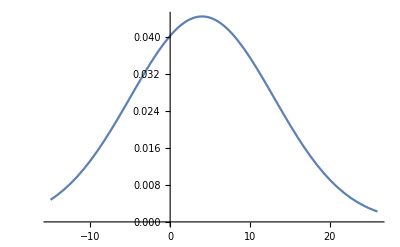

```mathematica
(*Получаемые значения могут использоваться в других функциях или выражениях. Например, при построении графика*)
Plot[PDF[NormalDistribution[4,9],x],{x,-15,26}]
```

```mathematica
(*Mean - находит среднее значение
BinomialDistribution[n,p] - представляет собой биномиальное распределение с n попытками и вероятностью успеха p*)
Mean[BinomialDistribution[150,.9]]
```

135.

```mathematica
(*CharacteristicFunction[dist, t] - дает характеристическую функцию для распределения dist как функцию переменной t
CauchyDistribution[a,b] - представляет собой распределение Коши с параметром местоположения a и параметром масштаба b*)
CharacteristicFunction[CauchyDistribution[a,b],t]
```

ⅇ^(ⅈ a t-b t Sign[t])

```mathematica
(*Moment[list,n] - находит n-й абсолютный момент
PoissonDistribution[μ] - представляет собой распределение Пуассона со средним значением μ*)
Moment[PoissonDistribution[μ],n]
```

Piecewise[{{BellB[n,μ], n≥0}, {0, True}}]

```mathematica
(*RandomVariate[dist,n] - дает возможность генерировать список n случайных чисел из распределения dist
ChiSquareDistribution[v] представляет собой распределение χ^2 с v степенями свободы*)
RandomVariate[ChiSquareDistribution[13],20]
```

{11.5733,11.7972,25.366,15.4032,22.7289,11.1939,13.6978,15.3222,16.7808,14.1531,10.7435,20.2856,8.76813,9.82378,10.2069,15.9071,16.7836,11.9835,8.74029,16.1922}

```mathematica
(*Геометрическое распределение описывает количество попыток до неудачи,где существует вероятность успеха p для каждой попытки*)
RandomVariate[GeometricDistribution[.6],20]
```

{0,0,1,2,1,1,0,4,0,2,0,0,0,0,0,1,0,0,1,1}

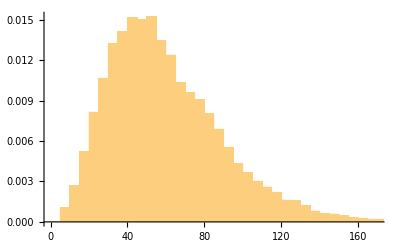

```mathematica
(*Сгенерируем 10000 чисел из гамма-распределения
GammaDistribution[α,β] - представляет собой гамма-распределение с параметром формы α и параметром масштаба β*)
data=RandomVariate[GammaDistribution[4,15],10000];
(* Histogram - строит гистограмму для значений по шкале плотности вероятности *)
hist=Histogram[data,Automatic,"ProbabilityDensity"]
```

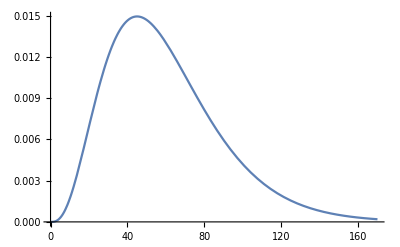

```mathematica
(*Для визуализации функции теоретической плотности можно использовать функцию Plot*)
p1=Plot[PDF[GammaDistribution[4,15],x],{x,0,170}]
```

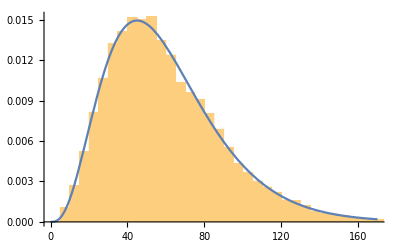

```mathematica
Show[hist, p1]
```

```mathematica
(*FindDistributionParameters - находит оценки параметров для распределения dist по данным data*)
alphabeta=FindDistributionParameters[data,GammaDistribution[α,β]]
```

{α→4.0359,β→14.8868}

```mathematica
(*При помощи EstimatedDistribution результаты могут быть сгруппированы в объект, представляющий собой распределение
EstimatedDistribution[data,dist] - оценивает параметрическое распределение dist по данным data*)
gdist=EstimatedDistribution[data,GammaDistribution[α,β]]
```

GammaDistribution[4.0359,14.8868]

```mathematica
(*Логарифмическое правдоподобие вычисляется при помощи функции LogLikelihood к оцениваемому распределению*)
LogLikelihood[gdist,data]
```

-47291.9

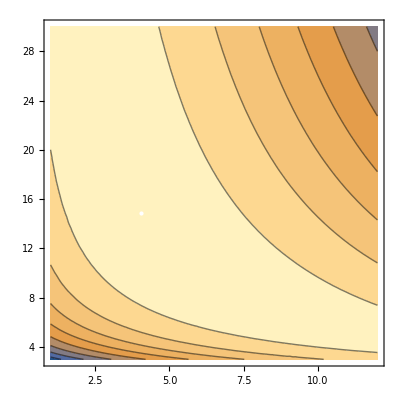

```mathematica
(*ContourPlot - оздание контурного графика в окрестности найденных значений, обеспечивающего в данной задаче качественное сравнение логарифмического правдоподобия. Белая точка находится в точке оптимума*)
ContourPlot[LogLikelihood[GammaDistribution[α,β],data],{α,1,12},{β,3,30},Epilog->{White,Point[{α,β}/.alphabeta]}]
```

```mathematica
3.Проверка гипотез о математическом ожидании
```

```mathematica
(*ExponentialDistribution[λ] - представляет собой экспоненциальное распределение с масштабом,обратно пропорциональным параметру λ*)
data = RandomReal[ExponentialDistribution[1/5], 20]
```

{7.28939,2.19071,12.594,0.845591,1.02454,1.19411,0.401268,4.22649,8.54825,4.45059,2.01681,1.9796,2.19876,2.03258,7.70507,12.7981,11.265,7.96373,12.0797,0.752754}

```mathematica
(*Загрузка пакета гипотез Hypothesis Testing Package
In = <<HypothesisTesting'*)
```

```mathematica
(*MeanTest - возвращает односторонее p-значение
In = MeanTest[data,6]
In = MeanTest[data,6, TwoSided->True] - позволяет получить двусторонее p-начение для этого же теста]*)
```

```mathematica
data2 = RandomReal[ExponentialDistribution[1/3], 20];
(* MeanDifferenceTest проверяет, будет ли разница между двумя математическими ожиданиями существенно отличаться от предполагаемого значения. Разностью является число после двух наборов данных*)
MeanDifferenceTest[data,data2,0]
MeanDifferenceTest[data,data2,4]
```

```mathematica
(*MeanTest - используется для тестов, выполняющихся для парных сравнений наборов данных*)
MeanTest[data-data2,0]
```

```mathematica
4.Работа со столбцами данных
```

```mathematica
(*BlockRandom[expr] фактически сохраняет состояния всех псевдослучайных генераторов перед вычислением expr,а затем восстанавливает их после.
SeedRandom[s] - сбрасывает псевдослучайный генератор,используя s в качестве начального числа.
RandomInteger[{a, b},{y,x}] - даёт массив размерностью y на x псевдослучайных чисел*)
data = BlockRandom[SeedRandom[6];RandomInteger[{1, 14},{4,3}]]
```

{{5,2,3},{8,4,11},{4,2,10},{11,2,9}}

```mathematica
(*Mathematica описывает данные путем группировки списков внутри другого списка. Каждый список интерпретируется как строка внутри матрицы данных:*)
MatrixForm[data]
```

(5 | 2 | 3
8 | 4 | 11
4 | 2 | 10
11 | 2 | 9)

```mathematica
(*Функция Grid отображает данные таким же самым образом, но без скобок:*)
Grid[data]
```

5 | 2 | 3
8 | 4 | 11
4 | 2 | 10
11 | 2 | 9

```mathematica
(*Найти среднее для каждого столбца можно с помощью Mean*)
Mean[data]
```

{7,5/2,33/4}

```mathematica
(*Среднеквадратичное для каждого столбца*)
StandardDeviation[data]
```

{√10,1,(√(155/3))/2}

```mathematica
(*Медиана для каждого столбца*)
Median[data]
```

{13/2,2,19/2}

```mathematica
(*Выбор отдельного столбца*)
data[[All,1]]
```

{5,8,4,11}

```mathematica
Mean[data[[All,1]]]
StandardDeviation[data[[All,1]]]
Median[data[[All,1]]]
```

7

√10

13/2

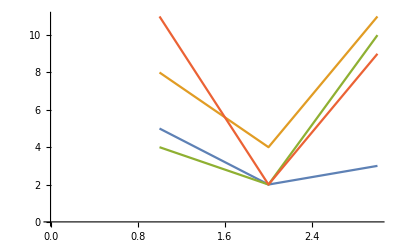

```mathematica
(*Для матриц, содержащих более двух столбцов, можно построить график как для отдельных наборов данных*)ListLinePlot[data]
```

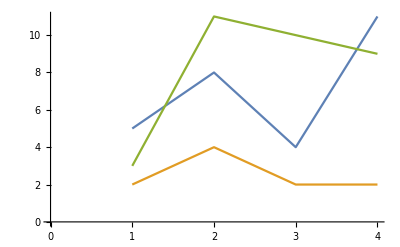

```mathematica
(*График можно построить и для транспонированных данных
Transpose[data] - транспонирует первые два уровня в списке data.*)
ListLinePlot[ Transpose[data]]
```

```mathematica
(*Map[f,expr] - применяет f к каждому элементу на первом уровне в expr
Normalize[v] - дает нормированную форму вектора v.*)
Map[Normalize,Transpose[data]]
```

{{5/(√226),4 √(2/113),2 √(2/113),11/(√226)},{1/(√7),2/(√7),1/(√7),1/(√7)},{3/(√311),11/(√311),10/(√311),9/(√311)}}

```mathematica
(*При повторном транспонировании мы получим матрицу с нормализованными столбцами*)
Transpose[%]
```

{{5/(√226),1/(√7),3/(√311)},{4 √(2/113),2/(√7),11/(√311)},{2 √(2/113),1/(√7),10/(√311)},{11/(√226),1/(√7),9/(√311)}}

```mathematica
(* Транспонирования и применение преобразований может выполняться для функций, которые выравнивают свой аргумент *)
Map[Max,Transpose[data]]
```

{11,4,11}

```mathematica
5.Выполнение операций с подгруппами данных
```

```mathematica
Пример 1
```

```mathematica
(* Данные ниже представляют собой количество проданной магазином продукции 3 видов от 2 производителей за определённый период*)
agdata={{milk,firmaB,132},{cheese,firmaB,140},{milk,firmaB,115},{icecream,firmaA,171},{milk,firmaA,145},{icecream,firmaB,138},{icecream,firmaB,171},{icecream,firmaA,169},{milk,firmaA,179},{cheese,firmaB,181},{milk,firmaA,186},{milk,firmaA,176},{milk,firmaA,182},{icecream,firmaA,164},{icecream,firmaB,165},{cheese,firmaA,174},{milk,firmaB,179},{cheese,firmaB,185},{icecream,firmaA,143},{cheese,firmaB,171}};
```

```mathematica
(*Сгруппировать данные можно при помощи GatherBy и First
GatherBy[data, f] - собирает в подсписки каждый набор элементов в списке data,который дает одно и то же значение при применении f
First[expr] - дает первый элемент в выражении expr.*)
bySoilType=GatherBy[agdata,First]
```

{{{milk,firmaB,132},{milk,firmaB,115},{milk,firmaA,145},{milk,firmaA,179},{milk,firmaA,186},{milk,firmaA,176},{milk,firmaA,182},{milk,firmaB,179}},{{cheese,firmaB,140},{cheese,firmaB,181},{cheese,firmaA,174},{cheese,firmaB,185},{cheese,firmaB,171}},{{icecream,firmaA,171},{icecream,firmaB,138},{icecream,firmaB,171},{icecream,firmaA,169},{icecream,firmaA,164},{icecream,firmaB,165},{icecream,firmaA,143}}}

```mathematica
(*Можно применить Table для вывода вида продукции и среднего количества их продаж*)
Table[{x[[1,1]],N[Mean[x[[All,-1]]]]},{x,bySoilType}]
```

{{milk,161.75},{cheese,170.2},{icecream,160.143}}

```mathematica
(*Для получения информации о количестве продаж в зависимости от производителя группировку данных необходимо выполнить по второму столбцу. Здесь применяется чистая функция #[[2]]*)
bySeedType=GatherBy[agdata,#[[2]]&]
```

{{{milk,firmaB,132},{cheese,firmaB,140},{milk,firmaB,115},{icecream,firmaB,138},{icecream,firmaB,171},{cheese,firmaB,181},{icecream,firmaB,165},{milk,firmaB,179},{cheese,firmaB,185},{cheese,firmaB,171}},{{icecream,firmaA,171},{milk,firmaA,145},{icecream,firmaA,169},{milk,firmaA,179},{milk,firmaA,186},{milk,firmaA,176},{milk,firmaA,182},{icecream,firmaA,164},{cheese,firmaA,174},{icecream,firmaA,143}}}

```mathematica
(*Если нам нужно вычислить среднее количество продаж для каждого производителя:*)
Table[{x[[1,2]],{N[Min[x[[All,-1]]]],N[Max[x[[All,-1]]]]}},{x,bySeedType}]
```

{{firmaB,{115.,185.}},{firmaA,{143.,186.}}}

```mathematica
(*Если нам нужно вычислить среднее количество продаж для продукции от каждого производителя:*)
Table[{x[[1,2]],{N[Min[x[[All,-1]]]],N[Max[x[[All,-1]]]]}},{x,bySeedType}]
```

{{firmaB,{115.,185.}},{firmaA,{143.,186.}}}

```mathematica
Пример 2
```

```mathematica
(*Список с информацией о виде лекарства*)
meddata={{drugB,67,18},{drugB,48,18},{drugA,33,16},{drugB,76,33},{drugB,33,3},{placebo,40,15},{drugB,78,28},{drugB,54,13},{placebo,46,23},{drugA,36,12},{drugA,69,30},{drugA,78,40},{placebo,77,37},{drugA,79,36},{drugA,45,16},{drugA,36,18},{drugA,58,24},{placebo,25,9},{drugB,75,25},{drugB,22,3},{placebo,51,25},{placebo,27,8},{placebo,47,20},{placebo,69,34},{drugB,52,16}};
```

```mathematica
(*Снова группировка данных по первому элементу для каждой строки*)
byDrug=GatherBy[meddata,First]
```

{{{drugB,67,18},{drugB,48,18},{drugB,76,33},{drugB,33,3},{drugB,78,28},{drugB,54,13},{drugB,75,25},{drugB,22,3},{drugB,52,16}},{{drugA,33,16},{drugA,36,12},{drugA,69,30},{drugA,78,40},{drugA,79,36},{drugA,45,16},{drugA,36,18},{drugA,58,24}},{{placebo,40,15},{placebo,46,23},{placebo,77,37},{placebo,25,9},{placebo,51,25},{placebo,27,8},{placebo,47,20},{placebo,69,34}}}

```mathematica
(* Можно создать функцию для получения размера выборки, среднего, медианы и диапазона для выбранного списка *)
describe[values_]:={Length[values],Mean[values],Median[values],{Min[values],Max[values]}}
```

```mathematica
(*Эту функцию можно применить внутри Table, чтобы получить статистические данные по виду лекарств(первый элемент)*)
Table[{x[[1,1]],describe[N[x[[All,-1]]]]},{x,byDrug}]
```

{{drugB,{9,17.4444,18.,{3.,33.}}},{drugA,{8,24.,21.,{12.,40.}}},{placebo,{8,21.375,21.5,{8.,37.}}}}

```mathematica
(*Группировку можно провести по возрасту(второй элемент) для каждых n лет(10 например*)
byAgeGroup=GatherBy[meddata,IntegerPart[#[[2]]/10]&]
```

{{{drugB,67,18},{drugA,69,30},{placebo,69,34}},{{drugB,48,18},{placebo,40,15},{placebo,46,23},{drugA,45,16},{placebo,47,20}},{{drugA,33,16},{drugB,33,3},{drugA,36,12},{drugA,36,18}},{{drugB,76,33},{drugB,78,28},{drugA,78,40},{placebo,77,37},{drugA,79,36},{drugB,75,25}},{{drugB,54,13},{drugA,58,24},{placebo,51,25},{drugB,52,16}},{{placebo,25,9},{drugB,22,3},{placebo,27,8}}}

```mathematica
(*Статистические данные можно получить теперь и в разрезе возрастных групп
Sort - сортирует данные в каноническом порядке (по возрастанию для чисел)*)
Table[{10IntegerPart[x[[1,2]]/10],describe[N[x[[All,-1]]]]},{x,byAgeGroup}]//Sort
```

{{20,{3,6.66667,8.,{3.,9.}}},{30,{4,12.25,14.,{3.,18.}}},{40,{5,18.4,18.,{15.,23.}}},{50,{4,19.5,20.,{13.,25.}}},{60,{3,27.3333,30.,{18.,34.}}},{70,{6,33.1667,34.5,{25.,40.}}}}

```mathematica
(*Пример группировки данных по виду лекарства и возрастной группе (1 и 2 элементы)*)
byDrugAndAgeGroup=GatherBy[meddata,{First[#],IntegerPart[#[[2]]/10]}&]
```

{{{drugB,67,18}},{{drugB,48,18}},{{drugA,33,16},{drugA,36,12},{drugA,36,18}},{{drugB,76,33},{drugB,78,28},{drugB,75,25}},{{drugB,33,3}},{{placebo,40,15},{placebo,46,23},{placebo,47,20}},{{drugB,54,13},{drugB,52,16}},{{drugA,69,30}},{{drugA,78,40},{drugA,79,36}},{{placebo,77,37}},{{drugA,45,16}},{{drugA,58,24}},{{placebo,25,9},{placebo,27,8}},{{drugB,22,3}},{{placebo,51,25}},{{placebo,69,34}}}

```mathematica
(*Данные в отсортированном виде поможет представить опять же Grid*)
Table[{x[[1,1]],10IntegerPart[x[[1,2]]/10],describe[N[x[[All,-1]]]]},{x,byDrugAndAgeGroup}]//Sort//Grid
```

drugA | 30 | {3,15.3333,16.,{12.,18.}}
drugA | 40 | {1,16.,16.,{16.,16.}}
drugA | 50 | {1,24.,24.,{24.,24.}}
drugA | 60 | {1,30.,30.,{30.,30.}}
drugA | 70 | {2,38.,38.,{36.,40.}}
drugB | 20 | {1,3.,3.,{3.,3.}}
drugB | 30 | {1,3.,3.,{3.,3.}}
drugB | 40 | {1,18.,18.,{18.,18.}}
drugB | 50 | {2,14.5,14.5,{13.,16.}}
drugB | 60 | {1,18.,18.,{18.,18.}}
drugB | 70 | {3,28.6667,28.,{25.,33.}}
placebo | 20 | {2,8.5,8.5,{8.,9.}}
placebo | 40 | {3,19.3333,20.,{15.,23.}}
placebo | 50 | {1,25.,25.,{25.,25.}}
placebo | 60 | {1,34.,34.,{34.,34.}}
placebo | 70 | {1,37.,37.,{37.,37.}}

```mathematica
6.Замена или удаление недостающих или недействительных данных
```

```mathematica
Пример 1
```

```mathematica
(*CountryData - возвращает валовой внутренний продукт для каждой страны, внесённой в перечень функции CountryData
";" в конце строки блокирует вывод на экран*)
gdps=Map[CountryData[#,"GDP"]&,CountryData[All]];
```

```mathematica
(*Take[list,n] - даёт первые n элементов из списка list*)
Take[gdps,10]
```

{1.91014×10^10 $,Missing[NotAvailable],1.52781×10^10 $,1.69988×10^11 $,6.36×10^8 $,3.15406×10^9 $,9.46354×10^10 $,2.11174×10^8 $,1.72776×10^9 $,4.49663×10^11 $}

```mathematica
(*Анализ некоторых данных может оказаться недоступным, например максимальный ВВП*)
Max[gdps]
```

Max::nord2: Comparison of 2.14277×10^13 and -∞ is invalid.

Max[Missing[NotAvailable],2.14277×10^13 $]

```mathematica
(*Отсутствие данных отображается словом Missing и его количество можно найти*)
Count[gdps,Missing["NotAvailable"]]
```

16

```mathematica
(*Общее количество данных в наборе также можно вычислить*)
Length[gdps]
```

249

```mathematica
(*DeleteCases[expr,pattern] -
удаляет все элементы в expr,соответствующие шаблону pattern*)
filteredgdps=DeleteCases[gdps,Missing["NotAvailable"]];
```

```mathematica
(*Теперь необходимо убедиться, что уменьшилось количество элементов в наборе данных, и том, что мы теперь можем найти максимум, который из-за отсутствующих значений не могли подсчитать*)
{Length[filteredgdps],Max[filteredgdps]}
```

{233,2.14277×10^13 $}

```mathematica
Пример 2
```

```mathematica
(*В наборе данных первый элемент - номер одной из двух групп, а второй и третий - численные результаты измерений свойств отдельных объектов в этих группах*)
data={{1,71.6,0.41},{2,27.2,4.96},{2,59.3,0.18},{1,46.,2.72},{2,42.2,1.06},{1,89.1,3.75},{4,88.6,1.9},{1,62.3,1.8},{1,82.7,"NA"},{1,35.5,1.84}};
```

```mathematica
(*Табличная форма поможет проще заметить проблемные данные*)
Grid[data,Dividers->All]
```

1 | 71.6 | 0.41
2 | 27.2 | 4.96
2 | 59.3 | 0.18
1 | 46. | 2.72
2 | 42.2 | 1.06
1 | 89.1 | 3.75
4 | 88.6 | 1.9
1 | 62.3 | 1.8
1 | 82.7 | NA
1 | 35.5 | 1.84

```mathematica
(*"|" - указывает на альтернативу для значений, между которыми находится
NumberQ проверяет, является ли аргумент числом
Выражение _?NumberQ является шаблоном для чисел
MatchQ[expr,pattern] - возвращает True, если форма шаблона pattern соответствует expr,и возвращает False в противном случае
Not - логическое "нет"*)
baddata[entry_]:=Not[MatchQ[entry,{1|2,_?NumberQ,_?NumberQ}]]
```

```mathematica
(*DeleteCases может воспользоваться данной функцией, чтобы удалить проблемные данные*)
DeleteCases[data,_?baddata]
```

```mathematica
{{1,71.6,0.41},{2,27.2,4.96},{2,59.3,0. или 21,46.,2.72},{2,42.2,1.06},{1,89.1,3.75},{1,62.3,1.8},{1,35.5,1.84}}
```

```mathematica
(*Можно задать функцию, определяющую является ли запись набора данных недействительной, путем проверки соответствия первого элемента записи значениям 1 или 2*)
```

```mathematica
badgroup[entry_]:=Not[MatchQ[entry[[1]],1|2]]
filtereddata=DeleteCases[data,_?badgroup]
```

{{1,71.6,0.41},{2,27.2,4.96},{2,59.3,0.18},{1,46.,2.72},{2,42.2,1.06},{1,89.1,3.75},{1,62.3,1.8},{1,82.7,NA},{1,35.5,1.84}}

```mathematica
(*Select - производит выборку элементов, в соответствии с заданным условием*)
group1=Select[filtereddata,#[[1]]===1&]
```

{{1,71.6,0.41},{1,46.,2.72},{1,89.1,3.75},{1,62.3,1.8},{1,82.7,NA},{1,35.5,1.84}}

```mathematica
(*Его можно использовать снова, но уже для выборки последнего элемента(это будет сделно, чтобы в будущем заменить значения NA данного стобца на среднее значение данного столбца*)
group1mean=Mean[Select[group1[[All,-1]],NumberQ]]
filtereddata[[All,3]]=filtereddata[[All,3]]/."NA"->group1mean
```

2.104

{0.41,4.96,0.18,2.72,1.06,3.75,1.8,2.104,1.84}

```mathematica
(*Посмотрим на отфильтрованные данные*)
Grid[filtereddata,Dividers->All]
```

1 | 71.6 | 0.41
2 | 27.2 | 4.96
2 | 59.3 | 0.18
1 | 46. | 2.72
2 | 42.2 | 1.06
1 | 89.1 | 3.75
1 | 62.3 | 1.8
1 | 82.7 | 2.104
1 | 35.5 | 1.84

```mathematica
(*Вместо шагов, проделанных выше, можно написать функцию
Сформулированная функция содержит аргументы: имя набора данных, еомер подлежащего обработке столбца, номер стобца для группировки и функцию, используемую для обоработки элементов столбца. Она группирует по заданному столбцу и заменяет любое нечисленное значение в обрабатываемом столбце результатом указанной функции*)
replaceByGroup[data_,col_,groupcol_,f_]:=Block[{columnvals,funvals,grouped,groups,rules},
columnvals=data[[All,{groupcol,col}]];
If[VectorQ[columnvals[[All,2]],NumericQ],
columnvals[[All,2]],
grouped=GatherBy[columnvals,First];
groups=grouped[[All,1,1]];
funvals=Table[f[Select[grouped[[i]][[All,2]],NumericQ]],{i,Length[groups]}];
rules=Table[Rule[{groups[[i]],_?(Not[NumericQ[#]]&)},{groups[[i]],funvals[[i]]}],{i,Length[groups]}];
Replace[columnvals,rules,{1}][[All,2]]]]
```

```mathematica
(*задаём данные повторно, но уже без записи с группой 4*)
newdata=DeleteCases[data,_?badgroup]
```

{{1,71.6,0.41},{2,27.2,4.96},{2,59.3,0.18},{1,46.,2.72},{2,42.2,1.06},{1,89.1,3.75},{1,62.3,1.8},{1,82.7,NA},{1,35.5,1.84}}

```mathematica
(*нахождение нечисленных значений в 3-ем столбце средним от соответствующей группы*)
replaceByGroup[newdata,3,1,Mean]
```

{0.41,4.96,0.18,2.72,1.06,3.75,1.8,2.104,1.84}

```mathematica
(*Как вариант, можно сделать такое и через использование медианы*)
replaceByGroup[newdata,3,1,Median]
```

{0.41,4.96,0.18,2.72,1.06,3.75,1.8,1.84,1.84}

```mathematica
(*Можно воспользоваться функцией Table для обработки набора данных столбец за столбцом*)
Grid[Transpose[Table[If[j==1,newdata[[All,j]],replaceByGroup[newdata,j,1,Mean]],{j,Length[newdata[[1]]]}]]]
```

1 | 71.6 | 0.41
2 | 27.2 | 4.96
2 | 59.3 | 0.18
1 | 46. | 2.72
2 | 42.2 | 1.06
1 | 89.1 | 3.75
1 | 62.3 | 1.8
1 | 82.7 | 2.104
1 | 35.5 | 1.84

```mathematica
(*Так как функция создана для обработки одного столбца, можно, например, недействительные элементы второго столбца зменить средним от соответствующей группы второго столбца, а недействительные элементы третьего - медианой от соответствующей группы третьего столбца*)
Grid[Transpose[{newdata[[All,1]],replaceByGroup[newdata,2,1,Mean],replaceByGroup[newdata,3,1,Median]}]]
```

1 | 71.6 | 0.41
2 | 27.2 | 4.96
2 | 59.3 | 0.18
1 | 46. | 2.72
2 | 42.2 | 1.06
1 | 89.1 | 3.75
1 | 62.3 | 1.8
1 | 82.7 | 1.84
1 | 35.5 | 1.84

```mathematica
7.Выполнение линейной регрессии
```

```mathematica
data = Table[{3 + i + RandomReal[{-3, 7}], i + RandomReal[{-2, 5}]}, {i, 1, 20}]
```

{{3.11033,5.59111},{10.8279,6.2399},{4.47841,6.82402},{12.9517,5.45815},{12.5882,6.52112},{8.33485,6.30574},{11.9256,6.38711},{16.3005,12.0817},{9.59703,13.4326},{13.5262,10.5084},{14.3134,9.13113},{12.5344,10.0752},{22.7791,11.2975},{20.992,14.9756},{16.2351,18.1625},{21.7772,15.259},{18.3761,20.9273},{23.6321,18.7597},{19.1728,21.822},{27.866,21.9534}}

```mathematica
(*LinearModelFit - создаёт линейную модель заданного набора данных*)
model=LinearModelFit[data,x,x]
```

FittedModel[1.7821+0.683896 x]

```mathematica
(*Извлечение функциональной формы моделизаданного набора данных*)
model["BestFit"]
```

1.7821+0.683896 x

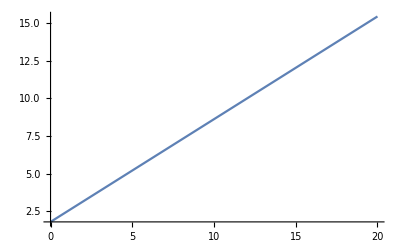

```mathematica
Plot[model["BestFit"], {x, 0, 20}]
```

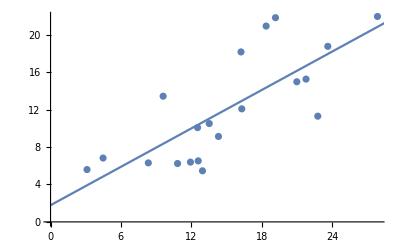

```mathematica
(*Отображение данных и линии вместе*)
Show[ListPlot[data], Plot[model["BestFit"], {x, 0, 30}]]
```

```mathematica
(*Получение информации по оценке параметров выполненной регресии*)
model["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.7821 | 2.235 | 0.797362 | 0.435633
x | 0.683896 | 0.136969 | 4.99308 | 0.0000942416

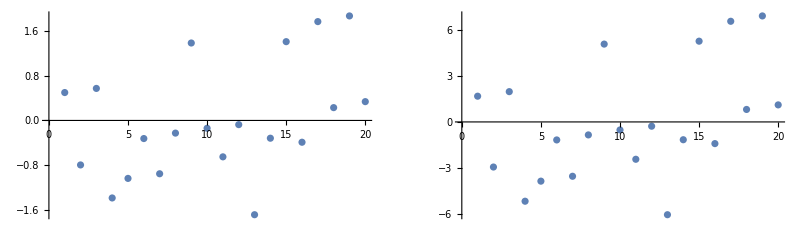

```mathematica
(*Извлечение и отображение на графике нормализованных и наблюдаемых невязок*)
{sr,fr}=model[{"StandardizedResiduals", "FitResiduals"}];
{{ListPlot[sr], ListPlot[fr]}}//GraphicsGrid
```

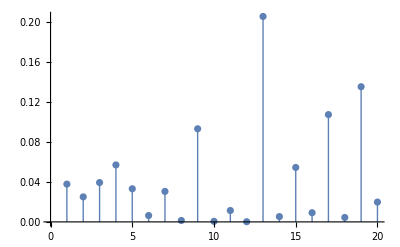

```mathematica
(*Построение графика расстояний Кука*)
ListPlot[model["CookDistances"], Filling->Axis, FillingStyle->Thick, PlotStyle->Thick]
```

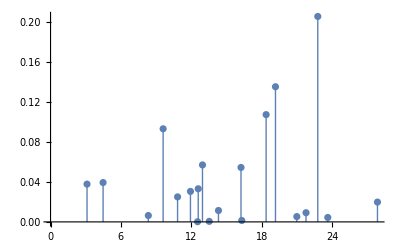

```mathematica
(*Построение графика расстояний Кука в зависимости от предикаторного значения*)
ListPlot[Transpose[{data[[All, 1]], model["CookDistances"]}], Filling->Axis, FillingStyle->Thick, PlotStyle->Thick]
```

```mathematica
(*Список доступных свойств для model*)
model["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}